Visualization of Jobs from the Cleaned Jobs dataset

```mathematica
SetDirectory[NotebookDirectory[]]               (* Setting directory, the dataset is also present here*)
```

C:\Users\ISHIKA GUPTA\Desktop\MSBA Subjects\Data Storytelling\BDI

```mathematica
FileNames[]
```

{BA_final (1).xlsx,BDI Visualization.nb,BI_Jobs_Final (1).xlsx,ch3_visal.nb,Chat enabled 2.nb,Chat enabled trial.nb,Checkpoint3_Visualization.nb,company_details,DA_final (1).xlsx,DE_final (1).xlsx,DS_final (1).xlsx,job_cleaned.csv,job_cleaned_new.csv,job_details,job_postings_2023_cleaned .ipynb,job_postings.csv,jobs.csv,JobsVisualization_chpt3.nb,layoffs_visualization.nb,maps,new attempt - Copy.nb,new attempt.nb,Trial.nb,Visualization of Jobs.nb}

```mathematica
job=Import["job_cleaned_new.csv"]              (* importing the cleaned jobs data*)
```

```mathematica
job//Dimensions          (* the data had 8 columns and 452 rows*)
```

{452,8}

--> Visualizing the density of job roles in different states of The US

```mathematica
location=Rest[job[[All,6]]]       (* Rest - all except header*)
```

{TN,KY,United States,NY,United States,NY,FL,TX,CT,FL,IL,FL,TX,United States,United States,AL,New York City Metropolitan Area,NY,TX,NY,TX,TX,United States,CA,IL,FL,TX,MA,MD,CA,AR,WA,OH,NY,TX,FL,UT,NJ,NE,United States,TX,United States,FL,MD,United States,NC,DC,SC,WI,VA,United States,NY,TX,NJ,United States,FL,United States,Tallahassee Metropolitan Area,NJ,United States,NY,Los Angeles Metropolitan Area,CA,TX,TX,United States,United States,WA,SC,NC,DC,United States,SC,New York Metropolitan Area,Cincinnati Metropolitan Area,TN,IL,United States,TX,NJ,United States,United States,CT,PA,MO,CA,TX,WA,MA,VA,CA,IL,United States,NY,WA,CT,IL,NY,United States,MO,WA,United States,MO,United States,Buffalo-Niagara Falls Area,New York City Metropolitan Area,TX,CA,IL,NJ,IL,United States,CA,United States,United States,United States,MI,Oklahoma City Metropolitan Area,Greater St. Louis,FL,United States,United States,MS,IN,TX,United States,WA,United States,MI,United States,Greater Pittsburgh Region,DC,United States,TX,TX,ME,OH,NC,United States,United States,Texas Metropolitan Area,TX,New York City Metropolitan Area,NY,TX,TN,OR,WI,CT,United States,FL,TN,VA,HI,United States,PA,NY,NE,IN,United States,VA,TN,NC,NY,NC,TX,CO,CA,GA,OH,CA,CA,MO,NC,NC,TN,CA,WA,IL,United States,United States,FL,Greater Minneapolis-St. Paul Area,NJ,New York City Metropolitan Area,United States,PA,NY,OK,United States,OR,OK,United States,CA,San Francisco Bay Area,CA,United States,CA,Utica-Rome Area,UT,NY,NM,TX,VA,United States,ME,United States,MA,United States,FL,United States,VA,United States,United States,TX,New York City Metropolitan Area,New York City Metropolitan Area,VA,New York City Metropolitan Area,UT,OH,United States,TX,CA,NY,NC,San Francisco Bay Area,United States,United States,NY,TX,CA,CA,MN,CT,TX,GA,CA,United States,United States,GA,GA,FL,TN,CO,IL,San Francisco Bay Area,MA,United States,CA,CA,NJ,ID,CA,CA,CA,TX,WA,WA,CA,CA,CA,WA,United States,OR,United States,DE,United States,CA,United States,CO,United States,United States,United States,United States,CA,United States,United States,WA,MI,United States,CA,CA,United States,MA,CA,San Francisco Bay Area,CA,TX,VA,United States,United States,GA,Charlotte Metro,United States,San Francisco Bay Area,United States,NC,United States,MD,Charlotte Metro,CA,CA,VA,United States,United States,CO,San Francisco Bay Area,TX,United States,TX,United States,CA,TX,NY,New York City Metropolitan Area,NY,CA,NC,MD,Atlanta Metropolitan Area,United States,NY,AZ,VA,CA,MI,NJ,MA,DE,CA,GA,FL,GA,United States,WA,Atlanta Metropolitan Area,MN,United States,United States,GA,United States,United States,IL,MI,New York City Metropolitan Area,TX,United States,TX,United States,United States,WI,VA,United States,United States,TX,GA,FL,GA,NAMER,MA,NC,United States,CT,United States,GA,IL,TN,FL,United States,OH,United States,KY,IL,CA,OH,OR,OR,AZ,GA,TX,TX,United States,CA,CA,FL,United States,FL,FL,United States,NY,CA,United States,United States,IL,VA,IL,TX,United States,GA,VA,San Francisco Bay Area,United States,OH,FL,IL,United States,CA,San Diego Metropolitan Area,TN,NJ,PA,FL,NC,TX,CA,CA,NC,United States,WA,Dallas-Fort Worth Metroplex,RI,TX,NC,NC,TX,United States,New York City Metropolitan Area,Atlanta Metropolitan Area,CA,United States,WA,AZ,United States,CA,VA,WA,United States,United States,AL,United States,United States,CA,FL,GA,IL,TX,United States,AZ,United States,TX}

```mathematica
Interpreter["USState"][location[[1]]]          (* Converting the text to a interpreted key....testing just for 1st value*)
```

Tennessee, United States

```mathematica
Table[Interpreter["USState"][i],{i,location}];       (* Converting all the text to interpreted keys*)
```

```mathematica
locationInterpreted=% ;     (* assigning a variable to the above result*)
```

```mathematica
locationClean=DeleteCases[locationInterpreted,_Failure] (* Deleting all the failed/missing values*)
```

{Tennessee, United States,Kentucky, United States,New York, United States,New York, United States,Florida, United States,Texas, United States,Connecticut, United States,Florida, United States,Illinois, United States,Florida, United States,Texas, United States,Alabama, United States,New York, United States,Texas, United States,New York, United States,Texas, United States,Texas, United States,California, United States,Illinois, United States,Florida, United States,Texas, United States,Massachusetts, United States,Maryland, United States,California, United States,Arkansas, United States,Washington, United States,Ohio, United States,New York, United States,Texas, United States,Florida, United States,Utah, United States,New Jersey, United States,Nebraska, United States,Texas, United States,Florida, United States,Maryland, United States,North Carolina, United States,District of Columbia, United States,South Carolina, United States,Wisconsin, United States,Virginia, United States,New York, United States,Texas, United States,New Jersey, United States,Florida, United States,New Jersey, United States,New York, United States,California, United States,Texas, United States,Texas, United States,Washington, United States,South Carolina, United States,North Carolina, United States,District of Columbia, United States,South Carolina, United States,Tennessee, United States,Illinois, United States,Texas, United States,New Jersey, United States,Connecticut, United States,Pennsylvania, United States,Missouri, United States,California, United States,Texas, United States,Washington, United States,Massachusetts, United States,Virginia, United States,California, United States,Illinois, United States,New York, United States,Washington, United States,Connecticut, United States,Illinois, United States,New York, United States,Missouri, United States,Washington, United States,Missouri, United States,Texas, United States,California, United States,Illinois, United States,New Jersey, United States,Illinois, United States,California, United States,Michigan, United States,Florida, United States,Mississippi, United States,Indiana, United States,Texas, United States,Washington, United States,Michigan, United States,District of Columbia, United States,Texas, United States,Texas, United States,Maine, United States,Ohio, United States,North Carolina, United States,Texas, United States,New York, United States,Texas, United States,Tennessee, United States,Oregon, United States,Wisconsin, United States,Connecticut, United States,Florida, United States,Tennessee, United States,Virginia, United States,Hawaii, United States,Pennsylvania, United States,New York, United States,Nebraska, United States,Indiana, United States,Virginia, United States,Tennessee, United States,North Carolina, United States,New York, United States,North Carolina, United States,Texas, United States,Colorado, United States,California, United States,Georgia, United States,Ohio, United States,California, United States,California, United States,Missouri, United States,North Carolina, United States,North Carolina, United States,Tennessee, United States,California, United States,Washington, United States,Illinois, United States,Florida, United States,New Jersey, United States,Pennsylvania, United States,New York, United States,Oklahoma, United States,Oregon, United States,Oklahoma, United States,California, United States,California, United States,California, United States,Utah, United States,New York, United States,New Mexico, United States,Texas, United States,Virginia, United States,Maine, United States,Massachusetts, United States,Florida, United States,Virginia, United States,Texas, United States,Virginia, United States,Utah, United States,Ohio, United States,Texas, United States,California, United States,New York, United States,North Carolina, United States,New York, United States,Texas, United States,California, United States,California, United States,Minnesota, United States,Connecticut, United States,Texas, United States,Georgia, United States,California, United States,Georgia, United States,Georgia, United States,Florida, United States,Tennessee, United States,Colorado, United States,Illinois, United States,Massachusetts, United States,California, United States,California, United States,New Jersey, United States,Idaho, United States,California, United States,California, United States,California, United States,Texas, United States,Washington, United States,Washington, United States,California, United States,California, United States,California, United States,Washington, United States,Oregon, United States,Delaware, United States,California, United States,Colorado, United States,California, United States,Washington, United States,Michigan, United States,California, United States,California, United States,Massachusetts, United States,California, United States,California, United States,Texas, United States,Virginia, United States,Georgia, United States,North Carolina, United States,Maryland, United States,California, United States,California, United States,Virginia, United States,Colorado, United States,Texas, United States,Texas, United States,California, United States,Texas, United States,New York, United States,New York, United States,California, United States,North Carolina, United States,Maryland, United States,New York, United States,Arizona, United States,Virginia, United States,California, United States,Michigan, United States,New Jersey, United States,Massachusetts, United States,Delaware, United States,California, United States,Georgia, United States,Florida, United States,Georgia, United States,Washington, United States,Minnesota, United States,Georgia, United States,Illinois, United States,Michigan, United States,Texas, United States,Texas, United States,Wisconsin, United States,Virginia, United States,Texas, United States,Georgia, United States,Florida, United States,Georgia, United States,Massachusetts, United States,North Carolina, United States,Connecticut, United States,Georgia, United States,Illinois, United States,Tennessee, United States,Florida, United States,Ohio, United States,Kentucky, United States,Illinois, United States,California, United States,Ohio, United States,Oregon, United States,Oregon, United States,Arizona, United States,Georgia, United States,Texas, United States,Texas, United States,California, United States,California, United States,Florida, United States,Florida, United States,Florida, United States,New York, United States,California, United States,Illinois, United States,Virginia, United States,Illinois, United States,Texas, United States,Georgia, United States,Virginia, United States,Ohio, United States,Florida, United States,Illinois, United States,California, United States,Tennessee, United States,New Jersey, United States,Pennsylvania, United States,Florida, United States,North Carolina, United States,Texas, United States,California, United States,California, United States,North Carolina, United States,Washington, United States,Rhode Island, United States,Texas, United States,North Carolina, United States,North Carolina, United States,Texas, United States,California, United States,Washington, United States,Arizona, United States,California, United States,Virginia, United States,Washington, United States,Alabama, United States,California, United States,Florida, United States,Georgia, United States,Illinois, United States,Texas, United States,Arizona, United States,Texas, United States}

```mathematica
countLocation=Counts[locationClean]
```

<|Tennessee, United States→9,Kentucky, United States→2,New York, United States→20,Florida, United States→21,Texas, United States→41,Connecticut, United States→6,Illinois, United States→16,Alabama, United States→2,California, United States→48,Massachusetts, United States→7,Maryland, United States→4,Arkansas, United States→1,Washington, United States→15,Ohio, United States→7,Utah, United States→3,New Jersey, United States→9,Nebraska, United States→2,North Carolina, United States→15,District of Columbia, United States→3,South Carolina, United States→3,Wisconsin, United States→3,Virginia, United States→14,Pennsylvania, United States→4,Missouri, United States→4,Michigan, United States→5,Mississippi, United States→1,Indiana, United States→2,Maine, United States→2,Oregon, United States→5,Hawaii, United States→1,Colorado, United States→4,Georgia, United States→14,Oklahoma, United States→2,New Mexico, United States→1,Minnesota, United States→2,Idaho, United States→1,Delaware, United States→2,Arizona, United States→4,Rhode Island, United States→1|>

```mathematica
GeoRegionValuePlot[countLocation ]
```

-Graphics-

```mathematica
GeoRegionValuePlot[countLocation,GeoRange->"Country",ColorFunction->"TemperatureMap",GeoLabels-> Automatic,(ImageSize-> Full )]
```

-Graphics-

--> Visualizing Sponsorship data vs each state

```mathematica
Sponsorship = Rest[job[[All,8]]]
```

{0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,1,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,1,0,0,1,1,1,1,0,0,1,1,0,0,1,0,0,0,0,1,0,0,0,0,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,0,0,1,0,1,1,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,0,0,1,1,1,0,0,0,1,0,0}

```mathematica
combinedList=Transpose[{location,Sponsorship}]
```

{{TN,0},{KY,0},{United States,0},{NY,1},{United States,0},{NY,0},{FL,0},{TX,0},{CT,0},{FL,0},{IL,0},{FL,1},{TX,0},{United States,0},{United States,1},{AL,1},{New York City Metropolitan Area,0},{NY,0},{TX,0},{NY,0},{TX,0},{TX,0},{United States,0},{CA,0},{IL,0},{FL,1},{TX,1},{MA,1},{MD,0},{CA,0},{AR,0},{WA,0},{OH,0},{NY,0},{TX,0},{FL,0},{UT,0},{NJ,0},{NE,1},{United States,0},{TX,0},{United States,0},{FL,1},{MD,0},{United States,0},{NC,0},{DC,1},{SC,0},{WI,0},{VA,0},{United States,0},{NY,0},{TX,0},{NJ,0},{United States,0},{FL,1},{United States,0},{Tallahassee Metropolitan Area,0},{NJ,0},{United States,0},{NY,0},{Los Angeles Metropolitan Area,0},{CA,0},{TX,0},{TX,0},{United States,0},{United States,0},{WA,0},{SC,1},{NC,1},{DC,0},{United States,0},{SC,0},{New York Metropolitan Area,0},{Cincinnati Metropolitan Area,0},{TN,0},{IL,1},{United States,0},{TX,1},{NJ,0},{United States,0},{United States,0},{CT,1},{PA,1},{MO,0},{CA,0},{TX,0},{WA,0},{MA,0},{VA,0},{CA,1},{IL,0},{United States,0},{NY,1},{WA,0},{CT,1},{IL,0},{NY,0},{United States,0},{MO,0},{WA,0},{United States,0},{MO,0},{United States,0},{Buffalo-Niagara Falls Area,0},{New York City Metropolitan Area,0},{TX,0},{CA,0},{IL,0},{NJ,0},{IL,0},{United States,0},{CA,0},{United States,0},{United States,1},{United States,0},{MI,1},{Oklahoma City Metropolitan Area,0},{Greater St. Louis,0},{FL,0},{United States,0},{United States,0},{MS,0},{IN,0},{TX,0},{United States,0},{WA,1},{United States,0},{MI,1},{United States,0},{Greater Pittsburgh Region,0},{DC,0},{United States,0},{TX,0},{TX,0},{ME,0},{OH,0},{NC,0},{United States,0},{United States,0},{Texas Metropolitan Area,1},{TX,0},{New York City Metropolitan Area,0},{NY,0},{TX,1},{TN,0},{OR,0},{WI,0},{CT,0},{United States,0},{FL,0},{TN,1},{VA,0},{HI,0},{United States,0},{PA,1},{NY,0},{NE,1},{IN,0},{United States,1},{VA,0},{TN,0},{NC,1},{NY,1},{NC,1},{TX,1},{CO,0},{CA,0},{GA,1},{OH,1},{CA,0},{CA,0},{MO,1},{NC,0},{NC,0},{TN,0},{CA,0},{WA,1},{IL,0},{United States,0},{United States,0},{FL,0},{Greater Minneapolis-St. Paul Area,1},{NJ,1},{New York City Metropolitan Area,1},{United States,0},{PA,0},{NY,0},{OK,1},{United States,1},{OR,0},{OK,0},{United States,0},{CA,0},{San Francisco Bay Area,0},{CA,0},{United States,0},{CA,1},{Utica-Rome Area,0},{UT,0},{NY,0},{NM,0},{TX,0},{VA,0},{United States,0},{ME,0},{United States,0},{MA,0},{United States,0},{FL,0},{United States,0},{VA,0},{United States,0},{United States,0},{TX,0},{New York City Metropolitan Area,0},{New York City Metropolitan Area,0},{VA,0},{New York City Metropolitan Area,0},{UT,0},{OH,0},{United States,1},{TX,0},{CA,1},{NY,1},{NC,0},{San Francisco Bay Area,0},{United States,0},{United States,0},{NY,0},{TX,0},{CA,0},{CA,0},{MN,0},{CT,0},{TX,0},{GA,0},{CA,0},{United States,0},{United States,0},{GA,1},{GA,0},{FL,0},{TN,0},{CO,0},{IL,1},{San Francisco Bay Area,1},{MA,0},{United States,0},{CA,0},{CA,0},{NJ,0},{ID,0},{CA,0},{CA,0},{CA,0},{TX,0},{WA,0},{WA,0},{CA,0},{CA,0},{CA,0},{WA,0},{United States,0},{OR,1},{United States,1},{DE,0},{United States,0},{CA,0},{United States,0},{CO,1},{United States,0},{United States,0},{United States,0},{United States,0},{CA,0},{United States,0},{United States,0},{WA,1},{MI,0},{United States,0},{CA,1},{CA,0},{United States,1},{MA,0},{CA,1},{San Francisco Bay Area,0},{CA,0},{TX,0},{VA,1},{United States,0},{United States,1},{GA,1},{Charlotte Metro,0},{United States,0},{San Francisco Bay Area,0},{United States,0},{NC,0},{United States,0},{MD,0},{Charlotte Metro,0},{CA,0},{CA,0},{VA,0},{United States,0},{United States,0},{CO,0},{San Francisco Bay Area,0},{TX,0},{United States,0},{TX,0},{United States,0},{CA,0},{TX,1},{NY,0},{New York City Metropolitan Area,0},{NY,1},{CA,1},{NC,0},{MD,0},{Atlanta Metropolitan Area,1},{United States,0},{NY,0},{AZ,1},{VA,0},{CA,1},{MI,1},{NJ,1},{MA,0},{DE,0},{CA,0},{GA,0},{FL,0},{GA,0},{United States,0},{WA,1},{Atlanta Metropolitan Area,0},{MN,1},{United States,0},{United States,0},{GA,0},{United States,0},{United States,0},{IL,0},{MI,0},{New York City Metropolitan Area,0},{TX,0},{United States,0},{TX,1},{United States,0},{United States,0},{WI,0},{VA,0},{United States,0},{United States,0},{TX,1},{GA,0},{FL,1},{GA,0},{NAMER,0},{MA,1},{NC,0},{United States,0},{CT,0},{United States,0},{GA,0},{IL,0},{TN,0},{FL,0},{United States,0},{OH,0},{United States,0},{KY,0},{IL,0},{CA,0},{OH,0},{OR,0},{OR,0},{AZ,0},{GA,1},{TX,0},{TX,1},{United States,0},{CA,0},{CA,1},{FL,0},{United States,0},{FL,0},{FL,0},{United States,0},{NY,0},{CA,0},{United States,1},{United States,1},{IL,1},{VA,0},{IL,0},{TX,0},{United States,0},{GA,0},{VA,0},{San Francisco Bay Area,0},{United States,1},{OH,0},{FL,0},{IL,1},{United States,0},{CA,0},{San Diego Metropolitan Area,0},{TN,0},{NJ,0},{PA,0},{FL,0},{NC,0},{TX,1},{CA,0},{CA,0},{NC,0},{United States,0},{WA,0},{Dallas-Fort Worth Metroplex,0},{RI,0},{TX,1},{NC,0},{NC,0},{TX,0},{United States,1},{New York City Metropolitan Area,0},{Atlanta Metropolitan Area,1},{CA,1},{United States,0},{WA,1},{AZ,1},{United States,0},{CA,1},{VA,0},{WA,1},{United States,0},{United States,0},{AL,0},{United States,0},{United States,0},{CA,1},{FL,1},{GA,1},{IL,0},{TX,0},{United States,0},{AZ,1},{United States,0},{TX,0}}

```mathematica
SponsoredgroupedData=GroupBy[combinedList,First->Last,Total]
```

<|TN→1,KY→0,United States→12,NY→5,FL→6,TX→10,CT→2,IL→4,AL→1,New York City Metropolitan Area→1,CA→11,MA→2,MD→0,AR→0,WA→6,OH→1,UT→0,NJ→2,NE→2,NC→3,DC→1,SC→1,WI→0,VA→1,Tallahassee Metropolitan Area→0,Los Angeles Metropolitan Area→0,New York Metropolitan Area→0,Cincinnati Metropolitan Area→0,PA→2,MO→1,Buffalo-Niagara Falls Area→0,MI→3,Oklahoma City Metropolitan Area→0,Greater St. Louis→0,MS→0,IN→0,Greater Pittsburgh Region→0,ME→0,Texas Metropolitan Area→1,OR→1,HI→0,CO→1,GA→5,Greater Minneapolis-St. Paul Area→1,OK→1,San Francisco Bay Area→1,Utica-Rome Area→0,NM→0,MN→1,ID→0,DE→0,Charlotte Metro→0,Atlanta Metropolitan Area→2,AZ→3,NAMER→0,San Diego Metropolitan Area→0,Dallas-Fort Worth Metroplex→0,RI→0|>

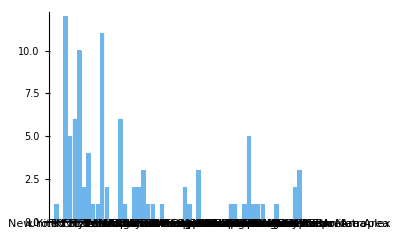

```mathematica
BarChart[SponsoredgroupedData,ChartLabels->Automatic,ChartStyle-> ColorData["Pastel"],ChartLabels->Placed[Automatic,Before],ImageSize->Full]
```

```mathematica
groupedData=GroupBy[combinedList,Last->First]
```

<|0→{TN,KY,United States,United States,NY,FL,TX,CT,FL,IL,TX,United States,New York City Metropolitan Area,NY,TX,NY,TX,TX,United States,CA,IL,MD,CA,AR,WA,OH,NY,TX,FL,UT,NJ,United States,TX,United States,MD,United States,NC,SC,WI,VA,United States,NY,TX,NJ,United States,United States,Tallahassee Metropolitan Area,NJ,United States,NY,Los Angeles Metropolitan Area,CA,TX,TX,United States,United States,WA,DC,United States,SC,New York Metropolitan Area,Cincinnati Metropolitan Area,TN,United States,NJ,United States,United States,MO,CA,TX,WA,MA,VA,IL,United States,WA,IL,NY,United States,MO,WA,United States,MO,United States,Buffalo-Niagara Falls Area,New York City Metropolitan Area,TX,CA,IL,NJ,IL,United States,CA,United States,United States,Oklahoma City Metropolitan Area,Greater St. Louis,FL,United States,United States,MS,IN,TX,United States,United States,United States,Greater Pittsburgh Region,DC,United States,TX,TX,ME,OH,NC,United States,United States,TX,New York City Metropolitan Area,NY,TN,OR,WI,CT,United States,FL,VA,HI,United States,NY,IN,VA,TN,CO,CA,CA,CA,NC,NC,TN,CA,IL,United States,United States,FL,United States,PA,NY,OR,OK,United States,CA,San Francisco Bay Area,CA,United States,Utica-Rome Area,UT,NY,NM,TX,VA,United States,ME,United States,MA,United States,FL,United States,VA,United States,United States,TX,New York City Metropolitan Area,New York City Metropolitan Area,VA,New York City Metropolitan Area,UT,OH,TX,NC,San Francisco Bay Area,United States,United States,NY,TX,CA,CA,MN,CT,TX,GA,CA,United States,United States,GA,FL,TN,CO,MA,United States,CA,CA,NJ,ID,CA,CA,CA,TX,WA,WA,CA,CA,CA,WA,United States,DE,United States,CA,United States,United States,United States,United States,United States,CA,United States,United States,MI,United States,CA,MA,San Francisco Bay Area,CA,TX,United States,Charlotte Metro,United States,San Francisco Bay Area,United States,NC,United States,MD,Charlotte Metro,CA,CA,VA,United States,United States,CO,San Francisco Bay Area,TX,United States,TX,United States,CA,NY,New York City Metropolitan Area,NC,MD,United States,NY,VA,MA,DE,CA,GA,FL,GA,United States,Atlanta Metropolitan Area,United States,United States,GA,United States,United States,IL,MI,New York City Metropolitan Area,TX,United States,United States,United States,WI,VA,United States,United States,GA,GA,NAMER,NC,United States,CT,United States,GA,IL,TN,FL,United States,OH,United States,KY,IL,CA,OH,OR,OR,AZ,TX,United States,CA,FL,United States,FL,FL,United States,NY,CA,VA,IL,TX,United States,GA,VA,San Francisco Bay Area,OH,FL,United States,CA,San Diego Metropolitan Area,TN,NJ,PA,FL,NC,CA,CA,NC,United States,WA,Dallas-Fort Worth Metroplex,RI,NC,NC,TX,New York City Metropolitan Area,United States,United States,VA,United States,United States,AL,United States,United States,IL,TX,United States,United States,TX},1→{NY,FL,United States,AL,FL,TX,MA,NE,FL,DC,FL,SC,NC,IL,TX,CT,PA,CA,NY,CT,United States,MI,WA,MI,Texas Metropolitan Area,TX,TN,PA,NE,United States,NC,NY,NC,TX,GA,OH,MO,WA,Greater Minneapolis-St. Paul Area,NJ,New York City Metropolitan Area,OK,United States,CA,United States,CA,NY,GA,IL,San Francisco Bay Area,OR,United States,CO,WA,CA,United States,CA,VA,United States,GA,TX,NY,CA,Atlanta Metropolitan Area,AZ,CA,MI,NJ,WA,MN,TX,TX,FL,MA,GA,TX,CA,United States,United States,IL,United States,IL,TX,TX,United States,Atlanta Metropolitan Area,CA,WA,AZ,CA,WA,CA,FL,GA,AZ}|>

```mathematica
zeroCounts=Counts[groupedData[0]]
```

<|TN→8,KY→2,United States→97,NY→15,FL→15,TX→31,CT→4,IL→12,New York City Metropolitan Area→9,CA→37,MD→4,AR→1,WA→9,OH→6,UT→3,NJ→7,NC→12,SC→2,WI→3,VA→13,Tallahassee Metropolitan Area→1,Los Angeles Metropolitan Area→1,DC→2,New York Metropolitan Area→1,Cincinnati Metropolitan Area→1,MO→3,MA→5,Buffalo-Niagara Falls Area→1,Oklahoma City Metropolitan Area→1,Greater St. Louis→1,MS→1,IN→2,Greater Pittsburgh Region→1,ME→2,OR→4,HI→1,CO→3,PA→2,OK→1,San Francisco Bay Area→6,Utica-Rome Area→1,NM→1,MN→1,GA→9,ID→1,DE→2,MI→2,Charlotte Metro→2,Atlanta Metropolitan Area→1,NAMER→1,AZ→1,San Diego Metropolitan Area→1,Dallas-Fort Worth Metroplex→1,RI→1,AL→1|>

```mathematica
oneCounts=Counts[groupedData[1]]
```

<|NY→5,FL→6,United States→12,AL→1,TX→10,MA→2,NE→2,DC→1,SC→1,NC→3,IL→4,CT→2,PA→2,CA→11,MI→3,WA→6,Texas Metropolitan Area→1,TN→1,GA→5,OH→1,MO→1,Greater Minneapolis-St. Paul Area→1,NJ→2,New York City Metropolitan Area→1,OK→1,San Francisco Bay Area→1,OR→1,CO→1,VA→1,Atlanta Metropolitan Area→2,AZ→3,MN→1|>

```mathematica
listForm0=Normal[zeroCounts]
```

{TN→8,KY→2,United States→97,NY→15,FL→15,TX→31,CT→4,IL→12,New York City Metropolitan Area→9,CA→37,MD→4,AR→1,WA→9,OH→6,UT→3,NJ→7,NC→12,SC→2,WI→3,VA→13,Tallahassee Metropolitan Area→1,Los Angeles Metropolitan Area→1,DC→2,New York Metropolitan Area→1,Cincinnati Metropolitan Area→1,MO→3,MA→5,Buffalo-Niagara Falls Area→1,Oklahoma City Metropolitan Area→1,Greater St. Louis→1,MS→1,IN→2,Greater Pittsburgh Region→1,ME→2,OR→4,HI→1,CO→3,PA→2,OK→1,San Francisco Bay Area→6,Utica-Rome Area→1,NM→1,MN→1,GA→9,ID→1,DE→2,MI→2,Charlotte Metro→2,Atlanta Metropolitan Area→1,NAMER→1,AZ→1,San Diego Metropolitan Area→1,Dallas-Fort Worth Metroplex→1,RI→1,AL→1}

```mathematica
listForm1=Normal[oneCounts]
```

{NY→5,FL→6,United States→12,AL→1,TX→10,MA→2,NE→2,DC→1,SC→1,NC→3,IL→4,CT→2,PA→2,CA→11,MI→3,WA→6,Texas Metropolitan Area→1,TN→1,GA→5,OH→1,MO→1,Greater Minneapolis-St. Paul Area→1,NJ→2,New York City Metropolitan Area→1,OK→1,San Francisco Bay Area→1,OR→1,CO→1,VA→1,Atlanta Metropolitan Area→2,AZ→3,MN→1}

```mathematica
result=Merge[{listForm0,listForm1},Ratio]
```

<|TN→Ratio[{8,1}],KY→Ratio[{2}],United States→Ratio[{97,12}],NY→Ratio[{15,5}],FL→Ratio[{15,6}],TX→Ratio[{31,10}],CT→Ratio[{4,2}],IL→Ratio[{12,4}],New York City Metropolitan Area→Ratio[{9,1}],CA→Ratio[{37,11}],MD→Ratio[{4}],AR→Ratio[{1}],WA→Ratio[{9,6}],OH→Ratio[{6,1}],UT→Ratio[{3}],NJ→Ratio[{7,2}],NC→Ratio[{12,3}],SC→Ratio[{2,1}],WI→Ratio[{3}],VA→Ratio[{13,1}],Tallahassee Metropolitan Area→Ratio[{1}],Los Angeles Metropolitan Area→Ratio[{1}],DC→Ratio[{2,1}],New York Metropolitan Area→Ratio[{1}],Cincinnati Metropolitan Area→Ratio[{1}],MO→Ratio[{3,1}],MA→Ratio[{5,2}],Buffalo-Niagara Falls Area→Ratio[{1}],Oklahoma City Metropolitan Area→Ratio[{1}],Greater St. Louis→Ratio[{1}],MS→Ratio[{1}],IN→Ratio[{2}],Greater Pittsburgh Region→Ratio[{1}],ME→Ratio[{2}],OR→Ratio[{4,1}],HI→Ratio[{1}],CO→Ratio[{3,1}],PA→Ratio[{2,2}],OK→Ratio[{1,1}],San Francisco Bay Area→Ratio[{6,1}],Utica-Rome Area→Ratio[{1}],NM→Ratio[{1}],MN→Ratio[{1,1}],GA→Ratio[{9,5}],ID→Ratio[{1}],DE→Ratio[{2}],MI→Ratio[{2,3}],Charlotte Metro→Ratio[{2}],Atlanta Metropolitan Area→Ratio[{1,2}],NAMER→Ratio[{1}],AZ→Ratio[{1,3}],San Diego Metropolitan Area→Ratio[{1}],Dallas-Fort Worth Metroplex→Ratio[{1}],RI→Ratio[{1}],AL→Ratio[{1,1}],NE→Ratio[{2}],Texas Metropolitan Area→Ratio[{1}],Greater Minneapolis-St. Paul Area→Ratio[{1}]|>

```mathematica
listFormResult=Normal[result]
```

{TN→Ratio[{8,1}],KY→Ratio[{2}],United States→Ratio[{97,12}],NY→Ratio[{15,5}],FL→Ratio[{15,6}],TX→Ratio[{31,10}],CT→Ratio[{4,2}],IL→Ratio[{12,4}],New York City Metropolitan Area→Ratio[{9,1}],CA→Ratio[{37,11}],MD→Ratio[{4}],AR→Ratio[{1}],WA→Ratio[{9,6}],OH→Ratio[{6,1}],UT→Ratio[{3}],NJ→Ratio[{7,2}],NC→Ratio[{12,3}],SC→Ratio[{2,1}],WI→Ratio[{3}],VA→Ratio[{13,1}],Tallahassee Metropolitan Area→Ratio[{1}],Los Angeles Metropolitan Area→Ratio[{1}],DC→Ratio[{2,1}],New York Metropolitan Area→Ratio[{1}],Cincinnati Metropolitan Area→Ratio[{1}],MO→Ratio[{3,1}],MA→Ratio[{5,2}],Buffalo-Niagara Falls Area→Ratio[{1}],Oklahoma City Metropolitan Area→Ratio[{1}],Greater St. Louis→Ratio[{1}],MS→Ratio[{1}],IN→Ratio[{2}],Greater Pittsburgh Region→Ratio[{1}],ME→Ratio[{2}],OR→Ratio[{4,1}],HI→Ratio[{1}],CO→Ratio[{3,1}],PA→Ratio[{2,2}],OK→Ratio[{1,1}],San Francisco Bay Area→Ratio[{6,1}],Utica-Rome Area→Ratio[{1}],NM→Ratio[{1}],MN→Ratio[{1,1}],GA→Ratio[{9,5}],ID→Ratio[{1}],DE→Ratio[{2}],MI→Ratio[{2,3}],Charlotte Metro→Ratio[{2}],Atlanta Metropolitan Area→Ratio[{1,2}],NAMER→Ratio[{1}],AZ→Ratio[{1,3}],San Diego Metropolitan Area→Ratio[{1}],Dallas-Fort Worth Metroplex→Ratio[{1}],RI→Ratio[{1}],AL→Ratio[{1,1}],NE→Ratio[{2}],Texas Metropolitan Area→Ratio[{1}],Greater Minneapolis-St. Paul Area→Ratio[{1}]}

```mathematica
values=Values[listFormResult]
```

{Ratio[{8,1}],Ratio[{2}],Ratio[{97,12}],Ratio[{15,5}],Ratio[{15,6}],Ratio[{31,10}],Ratio[{4,2}],Ratio[{12,4}],Ratio[{9,1}],Ratio[{37,11}],Ratio[{4}],Ratio[{1}],Ratio[{9,6}],Ratio[{6,1}],Ratio[{3}],Ratio[{7,2}],Ratio[{12,3}],Ratio[{2,1}],Ratio[{3}],Ratio[{13,1}],Ratio[{1}],Ratio[{1}],Ratio[{2,1}],Ratio[{1}],Ratio[{1}],Ratio[{3,1}],Ratio[{5,2}],Ratio[{1}],Ratio[{1}],Ratio[{1}],Ratio[{1}],Ratio[{2}],Ratio[{1}],Ratio[{2}],Ratio[{4,1}],Ratio[{1}],Ratio[{3,1}],Ratio[{2,2}],Ratio[{1,1}],Ratio[{6,1}],Ratio[{1}],Ratio[{1}],Ratio[{1,1}],Ratio[{9,5}],Ratio[{1}],Ratio[{2}],Ratio[{2,3}],Ratio[{2}],Ratio[{1,2}],Ratio[{1}],Ratio[{1,3}],Ratio[{1}],Ratio[{1}],Ratio[{1}],Ratio[{1,1}],Ratio[{2}],Ratio[{1}],Ratio[{1}]}

```mathematica
labels=Keys[listFormResult]
```

{TN,KY,United States,NY,FL,TX,CT,IL,New York City Metropolitan Area,CA,MD,AR,WA,OH,UT,NJ,NC,SC,WI,VA,Tallahassee Metropolitan Area,Los Angeles Metropolitan Area,DC,New York Metropolitan Area,Cincinnati Metropolitan Area,MO,MA,Buffalo-Niagara Falls Area,Oklahoma City Metropolitan Area,Greater St. Louis,MS,IN,Greater Pittsburgh Region,ME,OR,HI,CO,PA,OK,San Francisco Bay Area,Utica-Rome Area,NM,MN,GA,ID,DE,MI,Charlotte Metro,Atlanta Metropolitan Area,NAMER,AZ,San Diego Metropolitan Area,Dallas-Fort Worth Metroplex,RI,AL,NE,Texas Metropolitan Area,Greater Minneapolis-St. Paul Area}

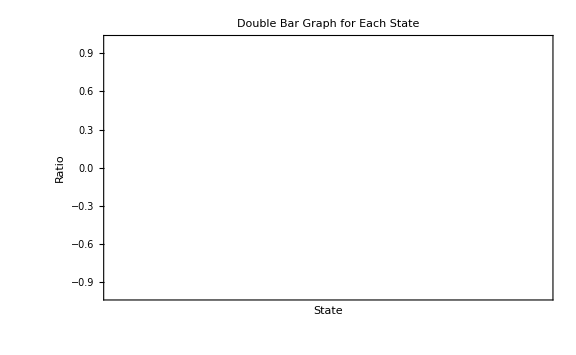

Keys::invrl: The argument zeroCounts is not a valid Association or a list of rules.

Lookup::invrl: The argument zeroCounts is not a valid Association or a list of rules.

Lookup::invrl: The argument oneCounts is not a valid Association or a list of rules.

```mathematica
BarChart[values,
  ChartLabels->{labels,None},
  ChartStyle->"Pastel",
  PlotLabel->"Double Bar Graph for Each State",
  FrameLabel->{"State","Ratio"},
  Frame->True,
  ImageSize->Large
]
```

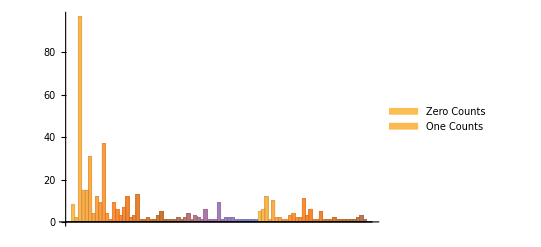

```mathematica
BarChart[{Values[listForm0],Values[listForm1]},ChartLabels->Automatic,ChartLegends->{"Zero Counts","One Counts"},ImageSize->Full] (*IGNORE THIS - DONT REMOVE*)
```

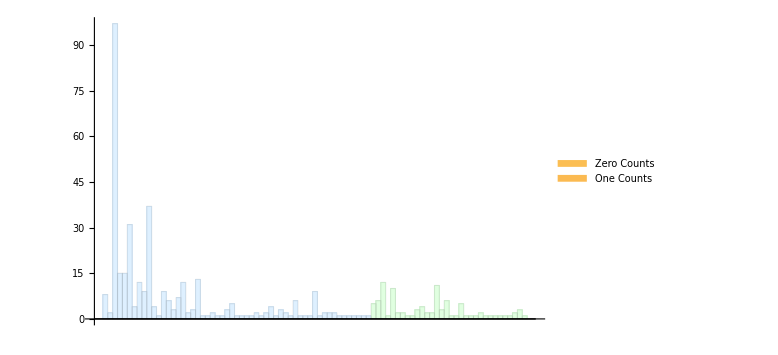

Transpose::nmtx: The first two levels of {{AL,AR,Atlanta Metropolitan Area,AZ,Buffalo-Niagara Falls Area,CA,Charlotte Metro,Cincinnati Metropolitan Area,CO,CT,«48»},{0,0}} cannot be transposed.

```mathematica
BarChart[{Style[Values[zeroCounts],LightBlue],Style[Values[oneCounts],LightGreen]},ChartLabels->Automatic,ChartLegends->{"Zero Counts","One Counts"},ImageSize->Large]  (*IGNORE THIS - DONT REMOVE*)
```